## The behavior of an imperfect predictor.

We have seen that this model performs well when it has the right parameters. But humans may have imperfect estimations of H. How does this affect the model?
You can play with the values of σ, hTrue, and hSubj to find out.

```mathematica
Remove["Global`*"]
```

### First, set the parameters.

```mathematica
μ=75;
σ=140;
hTrue=.05;
hSubj=.2;
m=200;
w=1366;
h=768;
```

### Then, generate some random data to simulate the behavior of the eggs in each trial.

```mathematica
r=RandomVariate[UniformDistribution[{0,1}],m];
```

```mathematica
switch=Table[If[r[[i]]>hTrue,0,1],{i,1,m}];
dist={};
val=1;
For[i=1,i≤m,i++,
If[switch[[i]]==1,
val=If[val==1,2,1]
];
dist=Append[dist,val]
]
x=Table[If[dist[[i]]==1,RandomVariate[NormalDistribution[μ,σ],1],RandomVariate[NormalDistribution[-μ,σ],1]],{i,1,m}];
x=Transpose[x]//Flatten;
(*y=Table[If[dist[[i]]==1,RandomVariate[NormalDistribution[0,σ],1],RandomVariate[NormalDistribution[0,σ],1]],{i,1,m}];
y=Transpose[y]//Flatten;

The code above lets egg placement vary in the y direction as much as it does in the x direction. Let's see what happens if we resrict y to a much smaller distribution:

*)
y=Table[If[dist[[i]]==1,RandomVariate[NormalDistribution[0,10],1],RandomVariate[NormalDistribution[0,10],1]],{i,1,m}];
y=Transpose[y]//Flatten;
```

Now, remove any points that aren’t in the center.

```mathematica
chicken=Table[{x[[i]],y[[i]],dist[[i]]},{i,1,m}]
```

{{311.337,11.2876,1},{-56.107,-7.11899,1},{-47.5246,0.440345,1},{261.726,-6.52984,1},{178.529,13.5775,1},{74.4589,20.0195,1},{-14.1517,2.52697,1},{249.598,-17.2827,1},{223.981,12.066,1},{207.299,-4.84555,1},{-16.9993,3.02356,1},{23.285,-3.71802,1},{183.677,0.422751,1},{-2.14817,1.45661,1},{11.0851,22.4737,1},{19.0049,-1.19211,1},{99.9303,4.37008,1},{346.017,-4.06178,1},{155.687,4.15913,1},{64.3126,-14.4261,1},{-152.418,12.0618,1},{50.222,12.257,1},{17.3065,1.86158,1},{57.8449,-8.56651,1},{-7.71834,-6.32434,1},{85.4935,-5.40415,1},{162.145,-6.9674,1},{-10.683,-24.3228,1},{141.553,3.60273,1},{84.3709,-0.676594,1},{-246.162,2.74593,1},{-73.9163,-1.40352,1},{217.914,2.51786,1},{41.444,-9.32825,1},{66.9593,10.9287,1},{124.861,-2.43069,1},{96.6545,-1.86494,1},{-65.6307,1.84477,1},{-37.6898,-9.84318,1},{75.8466,-11.892,1},{274.52,-15.5131,1},{83.5158,-5.60216,1},{-168.375,3.94397,2},{176.114,6.44055,1},{-28.7903,-1.29997,1},{300.822,-4.32756,1},{95.3142,-12.597,1},{-177.493,14.2098,2},{-155.23,-21.539,2},{79.8706,4.7828,2},{32.2207,-12.3743,2},{-96.402,16.0649,2},{-94.1294,-13.4883,2},{-160.341,0.257313,2},{-9.55028,1.34217,2},{-432.955,-18.1317,2},{137.771,8.0636,2},{-29.7036,-8.33882,2},{-139.825,5.25451,2},{-160.253,-8.88324,2},{-236.965,-18.0862,2},{29.653,3.19489,2},{-246.309,-2.26808,2},{-171.155,-1.55575,2},{-261.27,-8.0624,2},{-320.417,11.2542,2},{23.5769,-4.39615,2},{14.7911,-7.09338,2},{-239.042,7.46514,2},{42.4266,8.75655,2},{-144.928,5.68483,2},{-2.84319,-1.76073,2},{-114.258,2.8452,2},{-9.32202,13.3926,2},{-197.099,34.0937,2},{107.703,-8.91266,2},{2.61924,8.6286,2},{26.3613,3.56468,2},{-301.242,-13.0717,2},{-424.518,-21.2591,2},{-82.27,7.82405,2},{-211.821,16.738,2},{-127.367,-14.9065,2},{-76.5281,-13.3042,2},{-196.393,16.9812,2},{-18.8955,6.29085,2},{-116.308,6.17695,2},{-67.9079,-3.75213,2},{28.1008,-5.03118,2},{-142.166,5.23602,2},{-84.7658,2.37169,2},{-24.4143,-6.35932,2},{-44.8115,-6.28805,2},{-72.6755,1.47783,2},{145.604,-2.98034,2},{29.199,-0.953738,2},{-241.17,-7.39363,2},{-118.594,-14.7682,1},{-57.9907,-0.987612,1},{11.3757,1.14428,1},{-60.0765,3.61609,1},{153.953,-2.63841,1},{-17.0144,7.00821,1},{-90.2153,0.278852,1},{130.047,0.350541,1},{27.7729,24.5721,1},{29.4723,5.83818,1},{244.61,3.58887,1},{5.71726,-5.96811,1},{-98.8827,-1.92756,1},{120.482,-4.29014,1},{247.731,-1.68871,1},{27.6114,-9.99895,1},{99.4168,4.91721,1},{-28.5941,-10.1273,1},{150.368,2.66975,1},{-42.9267,9.13617,1},{-153.172,20.5306,2},{-123.722,-10.6897,2},{-57.7401,-5.30376,2},{-271.924,-7.06751,2},{79.5849,7.61271,2},{-11.9026,1.56896,2},{-137.08,-8.26885,2},{-16.9179,-8.61951,2},{283.068,12.8024,2},{-308.69,-17.878,2},{100.982,4.92807,2},{87.7053,-17.522,2},{-276.19,-1.79084,1},{19.6881,2.92415,1},{-50.5939,4.26648,1},{-45.9948,-3.39605,2},{243.479,-1.86785,2},{-25.6504,0.176666,2},{-106.2,6.91589,2},{70.3066,-6.01279,2},{-317.393,13.3491,2},{172.386,-8.7175,2},{-288.685,2.42804,2},{-6.41893,1.27811,2},{-294.325,-5.44493,2},{-5.82184,11.6225,2},{-177.903,4.29184,2},{-150.259,10.8985,2},{29.5412,-3.10152,2},{-340.151,-1.9742,2},{-17.3929,13.3962,2},{-57.1145,-10.69,2},{138.22,-1.76744,2},{-113.361,10.8622,2},{114.061,-2.25302,2},{117.918,12.2524,2},{-254.656,-0.685575,2},{-36.7893,-9.47256,2},{-152.823,-6.37953,2},{-180.722,2.73378,2},{29.447,0.854909,2},{-190.612,-3.01321,2},{69.831,2.69689,2},{-235.332,-5.08277,2},{-122.661,5.03163,2},{183.457,-27.1673,2},{132.488,-2.60988,2},{-160.699,-6.46559,2},{-96.1846,10.0779,2},{-6.78655,3.92295,2},{103.757,-3.623,2},{-155.337,3.82218,2},{-289.465,0.559594,2},{-77.6938,-7.12441,2},{-29.302,-8.95873,2},{60.7731,7.39145,2},{-298.245,7.58802,2},{-380.848,-2.85305,2},{-143.814,-0.0742434,2},{-373.013,10.0174,2},{-219.5,-4.10301,1},{285.551,7.11406,1},{260.195,0.441124,1},{-55.0767,6.57574,1},{-182.047,12.1459,1},{105.331,11.7793,1},{-97.6138,-8.55983,1},{154.409,4.39633,1},{290.133,-2.76074,1},{220.006,11.0341,1},{-158.193,-23.721,1},{167.905,1.23772,1},{117.368,-10.9689,1},{306.353,4.05335,1},{187.773,-7.52724,1},{-12.2821,2.34524,1},{-14.0884,0.159332,1},{12.4844,6.8409,1},{-12.6738,4.4328,1},{126.14,-16.7579,1},{155.6,-4.12647,1},{90.3161,-10.2164,1},{-74.0899,21.7107,1}}

```mathematica
chickCenter=Select[chicken,-75<#[[1]]<75&]
```

{{-56.107,-7.11899,1},{-47.5246,0.440345,1},{74.4589,20.0195,1},{-14.1517,2.52697,1},{-16.9993,3.02356,1},{23.285,-3.71802,1},{-2.14817,1.45661,1},{11.0851,22.4737,1},{19.0049,-1.19211,1},{64.3126,-14.4261,1},{50.222,12.257,1},{17.3065,1.86158,1},{57.8449,-8.56651,1},{-7.71834,-6.32434,1},{-10.683,-24.3228,1},{-73.9163,-1.40352,1},{41.444,-9.32825,1},{66.9593,10.9287,1},{-65.6307,1.84477,1},{-37.6898,-9.84318,1},{-28.7903,-1.29997,1},{32.2207,-12.3743,2},{-9.55028,1.34217,2},{-29.7036,-8.33882,2},{29.653,3.19489,2},{23.5769,-4.39615,2},{14.7911,-7.09338,2},{42.4266,8.75655,2},{-2.84319,-1.76073,2},{-9.32202,13.3926,2},{2.61924,8.6286,2},{26.3613,3.56468,2},{-18.8955,6.29085,2},{-67.9079,-3.75213,2},{28.1008,-5.03118,2},{-24.4143,-6.35932,2},{-44.8115,-6.28805,2},{-72.6755,1.47783,2},{29.199,-0.953738,2},{-57.9907,-0.987612,1},{11.3757,1.14428,1},{-60.0765,3.61609,1},{-17.0144,7.00821,1},{27.7729,24.5721,1},{29.4723,5.83818,1},{5.71726,-5.96811,1},{27.6114,-9.99895,1},{-28.5941,-10.1273,1},{-42.9267,9.13617,1},{-57.7401,-5.30376,2},{-11.9026,1.56896,2},{-16.9179,-8.61951,2},{19.6881,2.92415,1},{-50.5939,4.26648,1},{-45.9948,-3.39605,2},{-25.6504,0.176666,2},{70.3066,-6.01279,2},{-6.41893,1.27811,2},{-5.82184,11.6225,2},{29.5412,-3.10152,2},{-17.3929,13.3962,2},{-57.1145,-10.69,2},{-36.7893,-9.47256,2},{29.447,0.854909,2},{69.831,2.69689,2},{-6.78655,3.92295,2},{-29.302,-8.95873,2},{60.7731,7.39145,2},{-55.0767,6.57574,1},{-12.2821,2.34524,1},{-14.0884,0.159332,1},{12.4844,6.8409,1},{-12.6738,4.4328,1},{-74.0899,21.7107,1}}

```mathematica
x=chickCenter[[All,1]]
```

{-56.107,-47.5246,74.4589,-14.1517,-16.9993,23.285,-2.14817,11.0851,19.0049,64.3126,50.222,17.3065,57.8449,-7.71834,-10.683,-73.9163,41.444,66.9593,-65.6307,-37.6898,-28.7903,32.2207,-9.55028,-29.7036,29.653,23.5769,14.7911,42.4266,-2.84319,-9.32202,2.61924,26.3613,-18.8955,-67.9079,28.1008,-24.4143,-44.8115,-72.6755,29.199,-57.9907,11.3757,-60.0765,-17.0144,27.7729,29.4723,5.71726,27.6114,-28.5941,-42.9267,-57.7401,-11.9026,-16.9179,19.6881,-50.5939,-45.9948,-25.6504,70.3066,-6.41893,-5.82184,29.5412,-17.3929,-57.1145,-36.7893,29.447,69.831,-6.78655,-29.302,60.7731,-55.0767,-12.2821,-14.0884,12.4844,-12.6738,-74.0899}

```mathematica
y=chickCenter[[All,2]]
```

{-7.11899,0.440345,20.0195,2.52697,3.02356,-3.71802,1.45661,22.4737,-1.19211,-14.4261,12.257,1.86158,-8.56651,-6.32434,-24.3228,-1.40352,-9.32825,10.9287,1.84477,-9.84318,-1.29997,-12.3743,1.34217,-8.33882,3.19489,-4.39615,-7.09338,8.75655,-1.76073,13.3926,8.6286,3.56468,6.29085,-3.75213,-5.03118,-6.35932,-6.28805,1.47783,-0.953738,-0.987612,1.14428,3.61609,7.00821,24.5721,5.83818,-5.96811,-9.99895,-10.1273,9.13617,-5.30376,1.56896,-8.61951,2.92415,4.26648,-3.39605,0.176666,-6.01279,1.27811,11.6225,-3.10152,13.3962,-10.69,-9.47256,0.854909,2.69689,3.92295,-8.95873,7.39145,6.57574,2.34524,0.159332,6.8409,4.4328,21.7107}

```mathematica
dist=chickCenter[[All,3]]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,1,1,1,1,1,1,1,1,1,2,2,2,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,1,1,1,1,1}

```mathematica
m=Length[x]
```

74

### The following plot shows the x-coordinate of the egg in each trial

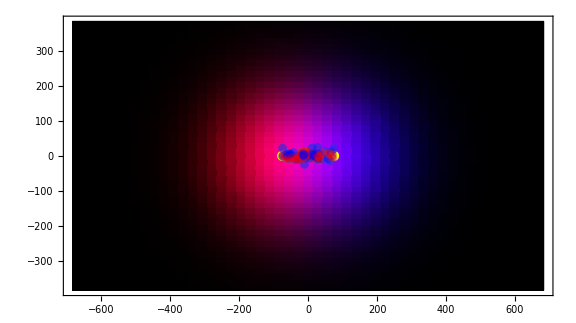

```mathematica
col=Table[If[dist[[i]]==1,Blue,Red],{i,1,m}];
pL[x_,y_]:=PDF[NormalDistribution[-μ,σ],x]* PDF[NormalDistribution[0,σ],y];
pR[x_,y_]:=PDF[NormalDistribution[μ,σ],x]* PDF[NormalDistribution[0,σ],y];
rFun[x_,y_]:=Round[pL[x,y]/pL[-μ,0],.001];
bFun[x_,y_]:=Round[pR[x,y]/pR[μ,0],.001];
cFun=Function[{x,y},RGBColor[rFun[x,y],0,bFun[x,y]]];
Show[
ParametricPlot[{x,y},{x,-w/2,w/2},{y,-h/2,h/2},ColorFunctionScaling->False,ColorFunction->cFun, Axes->False,PlotPoints->50, ImageSize->Large],
ListPlot[{{-μ,0},{μ,0}}, PlotStyle->Yellow],
ListPlot[Table[Style[{x[[i]],y[[i]]}, col[[i]]],{i,1,m}], PlotStyle->Opacity[.4]]
]
```

```mathematica
3*140
```

420

Following is a plot of the x-position of each egg over time. The color of each point marks which chicken is correct on that round.

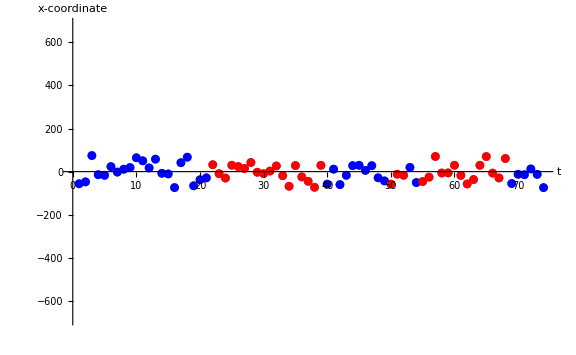

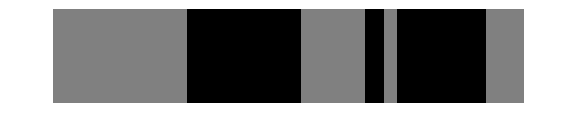

```mathematica
ListPlot[Table[Style[x[[i]], col[[i]]],{i,1,m}], PlotRange->{-683,683},Joined->False,AxesLabel->{"t","x-coordinate"}, ImageSize->Large]
ArrayPlot[{dist}, ImageSize->Large]
```

### Now, based on the data above, the model will make a prediction of which chicken the egg came from.

The model represents expected participant response based on their subjective H. The following simulates participant response using the model.

```mathematica
l[1]=0;
For[n=2,n≤m,n++,
ψ[n]=l[n-1]+Log[(1-hSubj)/hSubj+Exp[-l[n-1]]]-Log[(1-hSubj)/hSubj+Exp[l[n-1]]]//N;
llr[n]=-2*(LogLikelihood[NormalDistribution[μ,σ],{x[[n]]}]-LogLikelihood[NormalDistribution[-μ,σ],{x[[n]]}])//N;
l[n]=ψ[n]+llr[n];
]
```

```mathematica
Table[l[i],{i,1,m}]
```

{0,0.727417,-0.715246,-0.201104,0.13979,-0.272616,-0.130044,-0.247626,-0.438982,-1.24508,-1.45826,-1.04991,-1.48013,-0.67617,-0.2325,0.992272,-0.0688568,-1.06619,0.401635,0.815808,0.913304,0.0313512,0.164988,0.553496,-0.127125,-0.43708,-0.485994,-0.93735,-0.493586,-0.149662,-0.129781,-0.481288,0.00397299,1.04179,0.160548,0.469885,0.964536,1.6636,0.42157,1.13818,0.464349,1.19498,0.926295,0.106237,-0.387404,-0.318104,-0.612461,0.0774141,0.703474,1.29497,0.894861,0.773766,0.148492,0.863386,1.20214,1.06189,-0.475358,-0.183564,-0.0208311,-0.464659,-0.00939966,0.868562,1.06399,0.151094,-0.978296,-0.454437,0.178812,-0.823095,0.366448,0.406295,0.457286,0.0802538,0.242122,1.27885}

### The plot below demonstrates how the belief of the model changes over time in response to changes in the environment.

Below is a plot of Ln. This represents belief and the strength of the belief of which chicken is the correct chicken. The green dots represent correct answers and the red dots represent incorrect answers.

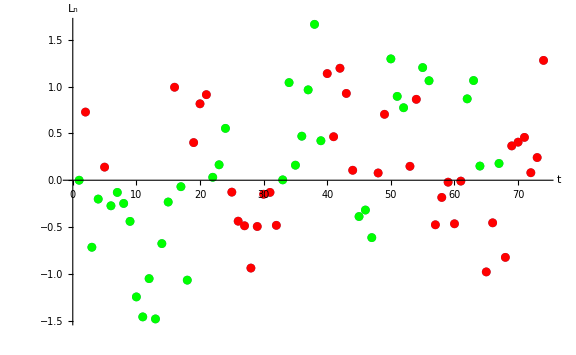

-Graphics-

```mathematica
pred=Table[If[l[i]>0,2,1],{i,1,m}];
col=Table[If[dist[[i]]==pred[[i]],Green,Red],{i,1,m}];
ListPlot[Table[Style[l[i],col[[i]]],{i,1,m}],Joined->False,AxesLabel->{"t","L_n"}, ImageSize->Large]
ArrayPlot[{dist}, ImageSize->Large]
```

```mathematica
pred=Table[If[l[i]>0,2,1],{i,1,m}];
```

### Percent correct:

```mathematica
Sum[If[dist[[i]]==pred[[i]],1,0],{i,1,m}]/m//N
```

0.5

### Histograms

We want to get a better idea of how H influences participant response. So, we plot the magnitude of ψ across trials as well as the magnitude of LLR across trials.

Below is a histogram of ψ across trials.

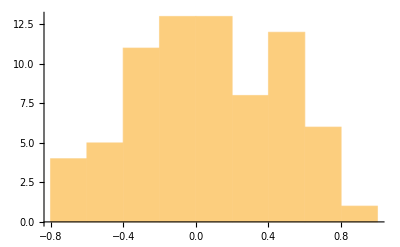

```mathematica
ψlist=Table[ψ[i],{i,2,m}];
Histogram[ψlist]
```

Below is a histogram of LLR across trials.

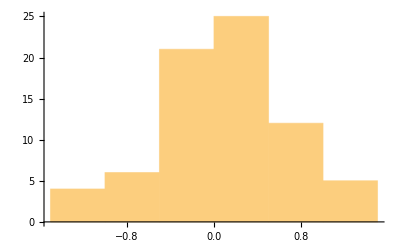

```mathematica
llrlist=Table[llr[i],{i,2,m}];
Histogram[llrlist]
```

Below is the above two plot overlaid.

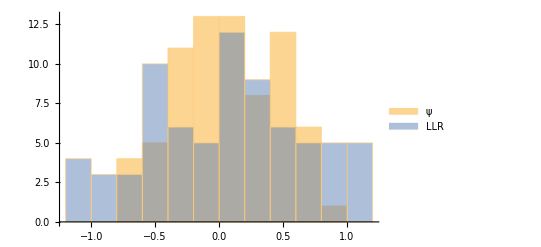

```mathematica
Histogram[{ψlist,llrlist},ChartLegends->{"ψ","LLR"}]
```

It appears that LLR tends to be higher in magnitude than ψ on average. To test this assumption, we look at the distribution of |ψ| - |LLR|. If ψ tends to have greater influence (magnitude) than LLR, then the Histogram will have many more positive values than negative.

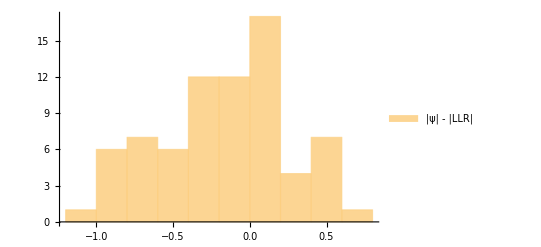

```mathematica
Histogram[{Abs[ψlist]-Abs[llrlist]},ChartLegends->{"|ψ| - |LLR|"}]
```

Note that with a small σ, it doesn’t matter how poor the prediction of H; the eggs appear so close to the chickens that H ends up having little influence on the decision. This is because LLR_n will always be larger in magnitude than ψ. Notice how the majority of the time, ψ does not influence the sign of Ln.

Below is shown the number of times adding ψ to the estimation did not affect the prediction.

```mathematica
Total[Table[If[TrueQ[Sign[ψ[n]+llr[n]]==Sign[llr[n]]],1,0],{n,2,m}]]/200//N
```

0.275